```mathematica
torDistancesAndTimes=Import["/home/twebb8/projects/cgal/c_curved_space/mathematica_tests/data_files/performance_data/torus_distance_and_time.csv"];
```

```mathematica
tableOfDistances = Table[torDistancesAndTimes[[i,1]],{i,Length[torDistancesAndTimes]}];
```

```mathematica
binnedDistances=BinLists[tableOfDistances,{0,10,.5}];(*this is the binning of the distances, but doesn't retain the time information -- we need to get indices to make this work*)
```

```mathematica
tableOfDistancesIndices = Table[Flatten[Table[Position[tableOfDistances,binnedDistances[[j,i]],3],{i,Length[binnedDistances[[j]]]}]],{j,Length[binnedDistances]}];
```

```mathematica
tableOfTimes = Table[Table[torDistancesAndTimes[[tableOfDistancesIndices[[j,i]],2]],{i,Length[tableOfDistancesIndices[[j]]]}],{j,Length[tableOfDistancesIndices]}];
```

```mathematica
timeAverages = Table[Mean[tableOfTimes[[i]]],{i,Length[tableOfTimes]-1}];
timeBins = Table[.25+(i-1)/2,{i,Length[timeAverages]}];
averagesWithBins = Table[{timeBins[[i]],timeAverages[[i]]},{i,Length[timeAverages]}];
logAveragesWithBins = Table[{timeBins[[i]],Log[timeAverages[[i]]]},{i,Length[timeAverages]}];
```

```mathematica
fitModel= LinearModelFit[averagesWithBins,{1,x},x];
nonLinearFitModel = NonlinearModelFit[averagesWithBins,x^a+b,{a,b},x];
r2line = fitModel["RSquared"]
r2power=nonLinearFitModel["RSquared"]
```

0.616885

0.999721

{FittedModel[49.9822+0.36256 x],0.616885,FittedModel[49.2527+x^0.609387],0.999721}

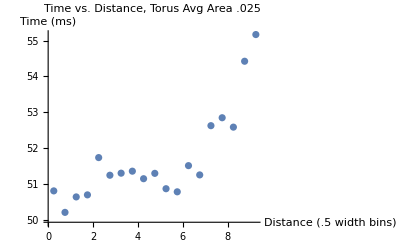

```mathematica
{fitModel,r2line,nonLinearFitModel,r2power}
forceFit = Plot[{fitModel[x],nonLinearFitModel[x]},{x,0,10}];
ttcDataPlot = ListPlot[averagesWithBins,PlotLabel->"Time vs. Distance, Torus Avg Area .025", AxesLabel->{"Distance (.5 width bins)","Time (ms)"}];
Show[ttcDataPlot]
```